# Recurrent Neural Networks optimization using Continual Evolution Algorithm in Mathematica Environment

Zdenek Buk (bukz1@fel.cvut.cz), http://cig.felk.cvut.cz

```mathematica
{{, }}
```

Department of Computer Science and Engineering
Faculty of Electrical Engineering
Czech Technical University in Prague

#### Initial settings

```mathematica
ind1={0.01,{0.34396853847176845,0.6275110604607965,-0.006861745388936635,0.7764976494143726,0.9165134875404312,-0.23610786194672043,0.18156001790203746,0.15257052282482061,0.007705622934316815,0.015355381600796145,1.7195007137841503,0.008558901429514279,0.4972783156020874,-3.66997822289293,0.17900545239749283,0.9921241982347185,0.0001913778291839692,0.7488416658646588,0.2863494330385875,0.006651587629076184,0.9858630787892518,0.09539612363935693,-0.026428185088357394,3.2139291437413746,0.6418945403174834,0.6110908233561249,0.5385990964586747,-0.016168113056978656,0.7253810527770522,0.041192253280306686,0.75035946284506,0.8111373215031111,0.6582386062263915,0.7527462906626883,0.04027087666026001,0.9068414527165412,0.22129734768662643,0.8266898509067746,0.6407211832426575,0.7210438415170345,0.44624223194998663,7.242256559492014*^-7},{1,1,0,0,1,0,0,0,0,0,0,1,0,1,0,0,0,0,1,0,0,0,1,1,0,1,0,1,1,0,1,1,1,1,0,1,1,0,1,1,1,1},{-0.009166668036795077,0.6201870007201289,0.008076470800591408,-0.0034418591220034267,0.02811851635378068,-0.007277118837452218,0.025551868400454134,-0.00021107049358140074,-8.329209471134389*^-6,-0.0003381625105574621,-0.0009427060904105792,-0.022326953989902382,-0.0009695352410322466,-3.6745576682850825,-0.00003014948141909993,-1.3889039689453192*^-6,-0.000036171757866886716,-0.00007212863493767129,0.27524760068681003,-0.00007074935613492836,0.000027353647309354678,-4.1041024606402615*^-6,-0.0264861721549725,3.2125137271247595,-0.000015162155764628824,0.6083075787888537,-0.00001490379211134516,-0.013215648456016502,0.7096830037903415,4.4260879688473805*^-6,0.7391096682440106,0.7850510134678879,0.6303622520859692,0.7263497003258074,0.0006992882524385654,0.9053497440437411,0.2212478662841126,-4.496423203485693*^-6,0.6382119033391097,0.7184114069790006,0.4437561790392903,0.0028444143689608818},{6}};
ind2={0,{0.46402466981119317,0.6275110604607965,-0.38712903006963617,0.2947251224164541,0.9165134875404312,0.35950805524686313,0.218732822868582,0.12509610873325525,0.5367598434902289,0.11922224560774458,0.5102137375727642,0.10298559064294478,5.886036042605149,0.061446417264578765,0.2609369300125767,0.035527162537994886,1.63177818998699,0.5511389721694656,0.22470088196336163,0.0773323040624626,0.7616678604365564,0.23860188381692135,0.019785847849154894,0.93409498272743,0.004536311271653544,0.6110908233561249,0.0035763060897439697,-0.37322349611360695,0.2744008691949984,-4.738886339994479,0.008317904817802925,0.004688771380544297,0.005434370631179797,-0.04898708145510525,0.039488424643413095,-0.020950769696050895,-0.07222740573236794,-1.9346959346024202,0.19654048526183437,0.6370660918037372,0.9094414251684737,0.32207243937227953},{1,1,0,0,1,1,1,0,0,0,1,0,1,1,1,0,1,1,0,1,0,0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,0,0,0,1,1,1},{0.46402466981119317,0.6275110604607965,-0.38712903006963617,0.2947251224164541,0.9165134875404312,0.35950805524686313,0.218732822868582,0.12509610873325525,0.5367598434902289,0.11922224560774458,0.5102137375727642,0.10298559064294478,5.886036042605149,0.061446417264578765,0.2609369300125767,0.035527162537994886,1.63177818998699,0.5511389721694656,0.22470088196336163,0.0773323040624626,0.7616678604365564,0.23860188381692135,0.019785847849154894,0.93409498272743,0.004536311271653544,0.6110908233561249,0.0035763060897439697,-0.37322349611360695,0.2744008691949984,-4.738886339994479,0.008317904817802925,0.004688771380544297,0.005434370631179797,-0.04898708145510525,0.039488424643413095,-0.020950769696050895,-0.07222740573236794,-1.9346959346024202,0.19654048526183437,0.6370660918037372,0.9094414251684737,0.32207243937227953},{6}};
```

|     ▶

## Introduction

A brief introduction to the problem, neural networks in general, and evolutionary algorithms.

### What?

Neural Networks

Adaptable, nature inspired, robust computational structures.

Ability to adapt to the specific problem (data).

### Why?

e.g. for Knowledge Discovery, Datamining

Motivation: Getting better models of real systems and data.

#### Classification

Classifies data into predefined categorical classes.

#### Clustering

Maps data item into one of several clusters, where clusters are grouping of data items based on similarity metrics.

#### Regression

Maps data item to a real - valued prediction variable.

#### Rule Generation

Extract classification rules from data, describes association relationship among different attributes.

#### Time Series Analysis

Models the states of the process generating the sequence, or extract and report deviation and trends over time.

### How?

How to adapt or how to create the neural network?

#### Optimization (Training) Methods

Gradient-based Methods

Evolutionary Algorithms

#### Two ways ...

Deductive approach

Inductive Approach

◀     |     ▶

## Neural Networks

There exist many types of Neural Networks. We can chose several criteria to  divide these types of the Neural Networks. One criteria could be e.g. the training algorithm. Another criteria could be the topology or structure of the Neural Network ...

### Feedforward Neural Networks

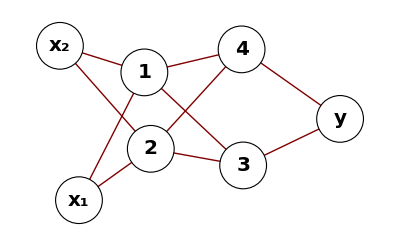

```mathematica
Clear[x,y];ff=GraphPlot[{Subscript[x, 1]->1,Subscript[x, 2]->2,Subscript[x, 1]->2,Subscript[x, 2]->1,1->3,1->4,2->3,2->4,3->y,4->y},VertexLabeling->True,DirectedEdges->True,Method->"SpringEmbedding",VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,0.2],Black,Text[Style[#2,Bold,20],#1]}&)]
```

### Recurrent Neural Networks

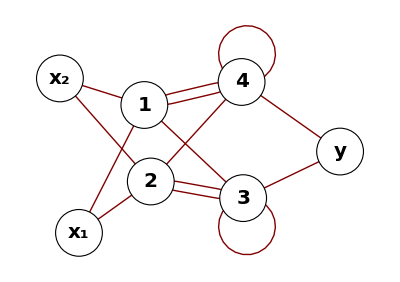

```mathematica
Clear[x,y];GraphPlot[{Subscript[x, 1]->1,Subscript[x, 2]->2,Subscript[x, 1]->2,Subscript[x, 2]->1,1->3,1->4,2->3,2->4,3->y,4->y,4->1,3->2,4->4,3->3},VertexLabeling->True,DirectedEdges->True,Method->"SpringEmbedding",VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,0.2],Black,Text[Style[#2,Bold,20],#1]}&)]
```

### Fully Recurrent Neural Networks

```mathematica
Clear[w];wm=Table[Subscript[w,i,j],{i,4},{j,6}];MatrixForm[wm]
```

(w_(1,1) | w_(1,2) | w_(1,3) | w_(1,4) | w_(1,5) | w_(1,6)
w_(2,1) | w_(2,2) | w_(2,3) | w_(2,4) | w_(2,5) | w_(2,6)
w_(3,1) | w_(3,2) | w_(3,3) | w_(3,4) | w_(3,5) | w_(3,6)
w_(4,1) | w_(4,2) | w_(4,3) | w_(4,4) | w_(4,5) | w_(4,6))

```mathematica
Clear[x];p=Flatten[MapIndexed[{#2⟦2⟧->#2⟦1⟧/.{5->Subscript[x, 1],6->Subscript[x, 2]},#1}&,wm,{2}],1];
```

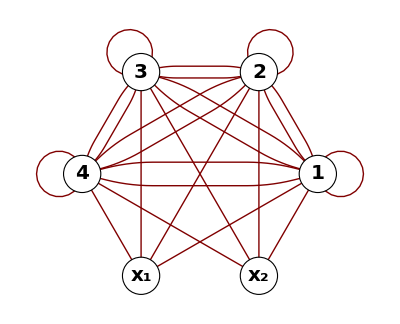

```mathematica
GraphPlot[p,VertexLabeling->True,DirectedEdges->True,Method->"CircularEmbedding",SelfLoopStyle->0.25,VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,0.1],Black,Text[Style[#2,Bold,20],#1]}&)]
```

◀     |     ▶

## Neural Networks Training

Using the training algorithm the Neural Network is adapted to given problem (data). Several approaches can be used - supervised or unsupervised training. The training algorithm can be used for adaptation of behavior of the network (by weight matrix modification) or for modification of the whole structure of the neural network.

### Adaptation of Behavior

The structure of the neural network stays unchanged, only weights of inter neuron connections (synapses) are modiffied during the training process.

### Adaptation of Structure and Topology

```mathematica
Clear[x,y];
sigg=Plot[1/(1+ⅇ^(-# x))&/@{0.5,1,2},{x,-5,5},PlotStyle->Thickness[0.02],ImageSize->100];
ff=GraphPlot[{Subscript[x, 1]->sigg,Subscript[x, 2]->sigg,Subscript[x, 3]->sigg,Subscript[x, 4]->sigg,sigg->y},VertexLabeling->True,DirectedEdges->True,VertexCoordinateRules->{Subscript[x, 1]->{0,Automatic},Subscript[x, 2]->{0,Automatic},Subscript[x, 3]->{0,Automatic},Subscript[x, 4]->{0,Automatic},y->{3,0.5},sigg->{1.4,0.5}},VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,If[#2==sigg,0.9,0.2]],Black,Text[Style[#2,Bold,20],#1]}&),ImageSize->300]
```

-Graphics-

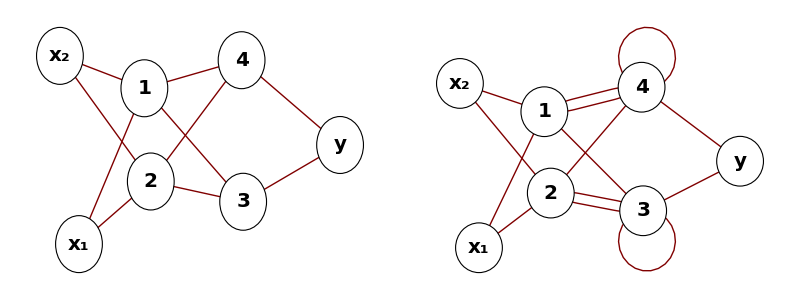

◀     |     ▶

## Continual Evolution Algorithm

Modification of standard genetic algorithm.

### Motivation

Inspiration in nature. Individuals in nature are born with some "parameters" (e.g. one head, two legs, etc.) that stays constant during the life. There are also some "parameters" that are modified during life - behavior, or knowledge ... these parameters are modified by learning (training algorithm), but at the beginning these parameters are initialized by some "default values" which we call instinct.

Goal : Evolution of structure and behavior of the Neural Networks (models in general) in one algorithm but separately (using different methods).

#### Basic characteristics of CEA

Optimization method based on population evolution.

Hybrid genetic algorithm - combination of genetic and gradient-based methods.

Uses separate evolution of structure and parameters (behavior) of model (network).

Variable population size.

"Age" parameter of the individuals.

Separated encoding of structure and behavior.

### Principles

#### Evolution in two dimensions

#### Probability Functions

Raw Death Probability

Raw Reproduction Probability

#### Balancing Functions

```mathematica
{{-Graphics3D-, -Graphics3D-}}
```

#### Evolution Process

◀     |     ▶

## CEA@@FRNNet

### Implementation

#### Encoding

Every individual is encoded into three main vectors - structural, behavioral, and parametric. The parametric vector (instinct) is used for initialization of behavioral vector.

Every individual also contains the age parameter.

individual={age, {p}, {s}, {b}}

#### Mutation and crossover

```mathematica
crossfunction[x1_,x2_]:=Module[
      {ind=x1,p1,p2,s1,s2,b1,b2,p,s,b,v,one,zero,idx,idxS,stmp,bRand,pr1,pr2,br1,br2,n},
      {p1,s1,b1}=Take[x1,{2,4}];
      {p2,s2,b2}=Take[x2,{2,4}];
      v=Length[s1];
      one=Table[1,{v}];
      zero=Table[0,{v}];
      n=Length[p1];
      pr1=Random[Real,{-0.1,0.1}]+#&/@p1;
      pr2=Random[Real,{-0.1,0.1}]+#&/@p2;
      br1=Random[Real,{-0.1,0.1}]+#&/@b1;
      br2=Random[Real,{-0.1,0.1}]+#&/@b2;
      idx=Table[Random[Integer,{1,8}],{n}];
      idxS=Table[Random[Integer,{1,4}],{n}];
b=p=#[[1]][[#[[2]]]]&/@Transpose[{Transpose[{p1,b1,p2,b2,pr1,br1,pr2,br2}],idx}];
      stmp=#[[1]][[#[[2]]]]&/@Transpose[{Transpose[{s1,s1,s2,s2}],idxS}];
      s=#[[Random[Integer,{1,7}]]]&/@
          Transpose[{stmp,stmp,stmp,stmp,stmp,one,zero}];
      ind[[1]]=0; ind[[2]]=p; ind[[3]]=s; ind[[4]]=b;
      ind
      ];
```

An example of reproduction (crossover) operation :

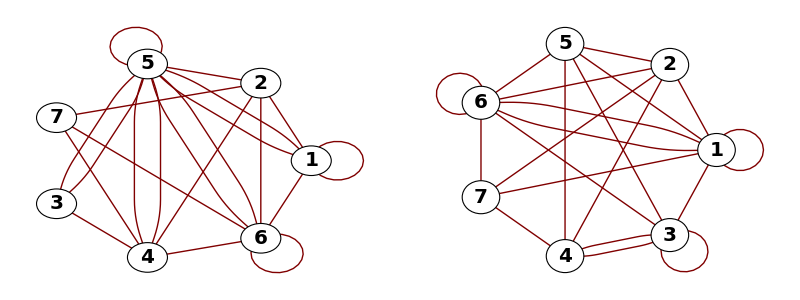

```mathematica
wm1s=Partition[ind1[[3]],Length[ind1[[3]]]/ind1[[5,1]]];
wm1p=Partition[ind1[[4]],Length[ind1[[4]]]/ind1[[5,1]]];
wm1=wm1s*wm1p;
Clear[x];p1=Cases[Flatten[MapIndexed[{#2⟦2⟧->#2⟦1⟧,#1}&,wm1,{2}],1],{_->_,_?(#≠0&)}];
wm2s=Partition[ind2[[3]],Length[ind2[[3]]]/ind2[[5,1]]];
wm2p=Partition[ind2[[4]],Length[ind2[[4]]]/ind2[[5,1]]];
wm2=wm2s*wm2p;
Clear[x];p2=Cases[Flatten[MapIndexed[{#2⟦2⟧->#2⟦1⟧,#1}&,wm2,{2}],1],{_->_,_?(#≠0&)}];
gp1=GraphPlot[p1,VertexLabeling->True,DirectedEdges->True,EdgeLabeling->False,Method->"CircularEmbedding",SelfLoopStyle->0.25,VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,0.1],Black,Text[Style[#2,Bold,20],#1]}&),ImageSize->250];
gp2=GraphPlot[p2,VertexLabeling->True,DirectedEdges->True,EdgeLabeling->False,Method->"CircularEmbedding",SelfLoopStyle->0.25,VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,0.1],Black,Text[Style[#2,Bold,20],#1]}&),ImageSize->250];
Grid[{{gp1,gp2}}]
```

```mathematica
ind3=crossfunction[ind1,ind2];
```

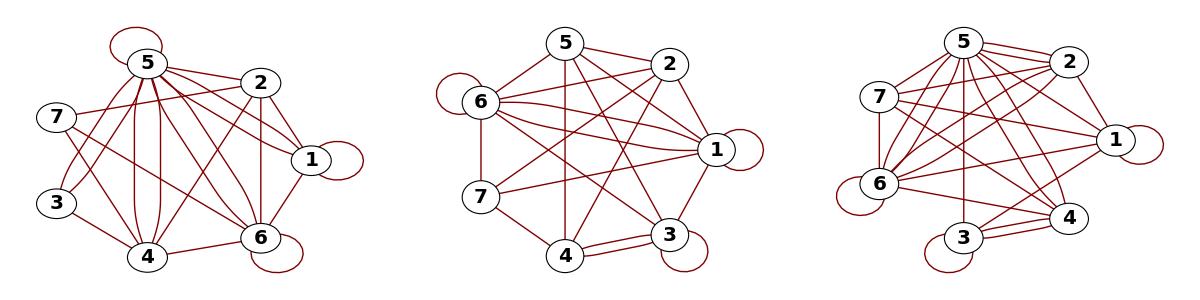

```mathematica
wm3s=Partition[ind3[[3]],Length[ind3[[3]]]/ind3[[5,1]]];
wm3p=Partition[ind3[[4]],Length[ind3[[4]]]/ind3[[5,1]]];
wm3=wm3s*wm3p;
Clear[x];p3=Cases[Flatten[MapIndexed[{#2⟦2⟧->#2⟦1⟧,#1}&,wm3,{2}],1],{_->_,_?(#≠0&)}];
gp3=GraphPlot[p3,VertexLabeling->True,DirectedEdges->True,EdgeLabeling->False,Method->"CircularEmbedding",SelfLoopStyle->0.25,VertexRenderingFunction->({EdgeForm[Black],White,Disk[#1,0.1],Black,Text[Style[#2,Bold,20],#1]}&),ImageSize->250];
Grid[{{gp1,gp2,gp3}}]
```

### Library

#### Probability functions

```mathematica
CEARawDP[a_, f_]
CEARawRP[a_, f_]
```

```mathematica
CEABalDP[n_, dp_]
CEABalRP[n_, rp_]
```

#### Individual creation

```mathematica
CEARandomIndividual[u_, v_, info_]
```

```mathematica
CEACreateIndividuals[n_, u_, v_, info_]
```

#### Initialization of CEA algorithm

```mathematica
CEAInitialize[n_, minn_, maxn_, dt_, u_, v_, ff_, crossf_, gradf_, updatef_, info_]
```

#### Evaluation and reproduction

```mathematica
CEAEvaluatePopulation[p_]
```

```mathematica
CEAReproduction[p_]
```

#### Debug

```mathematica
CEAPrintPopulation[p_]
```

#### Example

```mathematica
(* number of neurons *)
n=nn;
(* number of external inputs *)
m=0;
(* final matrix size: (n)x(n+m+1) *)
u=v=n (n+m+1);
pop=CEAInitialize[10,2,40,0.01,u,v,fitness,
crossfunction,gradf,updatef,
{n}];
fitnessCount=0;
```

```mathematica
CEAPrintPopulation[pop]
```

"Population size = 10 (0.210526)"

"Age" | "Fitness" | "DP" | "RP" | "s"
0 | 0.587735 | 0. | 0.184876 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0
0 | 0.586875 | 0. | 0.184674 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0.573039 | 0. | 0.181464 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0.572809 | 0. | 0.181411 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1
0 | 0.566947 | 0. | 0.180075 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0.56116 | 0. | 0.17877 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 1
0 | 0.560001 | 0. | 0.17851 | 1 | 1 | 0 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0.527281 | 0. | 0.171395 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1
0 | 0.480292 | 0. | 0.161926 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1
0 | 0.452752 | 0. | 0.156786 | 1 | 1 | 1 | 1 | 0 | 1 | 1 | 0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 1

### Testing

Testing the CEA with Fully Recurrent Neural Networks.

#### Experiment

"Learn to oscillate" - Training the FRNNet to generate the predefined sequence.

```mathematica
fitness[ind_] := Module[
   {n, s, b, v, u, w, x, y, z, err, fit, oldP, oldY},
   fitnessCount = fitnessCount + 1;
   v = Length[ind[[3]]];
   u = Length[ind[[4]]];
   
   nneurons = ind[[5, 1]];
   ninputs = v/nneurons - nneurons;
   
   s = Partition[ind[[3]], v/nneurons];
   b = Partition[ind[[4]], u/nneurons];
   
   y = Table[0, {nneurons}];
   err = 0;
   
   For[time = 0, time < Dimensions[tY][[1]],
    oldP = p;
    oldY = y;
    x = Prepend[tX[[time + 1]], 1];
    z = Join[y, x];
    w = s*b;
    y = sigmoid[#] & /@ (w.z);
    dk = tY[[time + 1]];
    (* Chyba se pocita z minuleho vystupu *)
ek=Plus @@(Abs[calcErr[#]] & /@ Transpose[{dk, oldY}]);
    err = err + ek;
    time++
    ]; (* for-loop time *)
   
   fit = 1 - err/maxErr;
   (*Print["fitness="<>ToString[fit]];*)
   fit
   ];
```

#### Batch Mode

We have created a bash script to generate the experiments (with different configurations) and for running the mathematica in batch mode.

### Results

```mathematica
For[i=0,i<20,
i++,
Print["Iteration = "<>ToString[i]];
pop=CEAReproduction[pop];
CEAPrintPopulation[pop]
]
```

Iteration = 0

Population size = 28

Age | Fitness | DP | RP
0 | 0.975697 | 0. | 0.6
0 | 0.975473 | 0. | 0.6
0.01 | 0.974421 | 0. | 0.600127

Iteration = 1

Population size = 47

Age | Fitness | DP | RP
0.01 | 0.975697 | 0. | 0.177904
0.01 | 0.975473 | 0. | 0.177904
0.02 | 0.974421 | 0. | 0.18276

Iteration = 2

Population size = 53

Age | Fitness | DP | RP
0.02 | 0.975697 | 0. | 0.0494266
0.02 | 0.975473 | 0. | 0.0494266
0 | 0.974533 | 0. | 0.0444444

Iteration = 3

Population size = 57

#### Training set

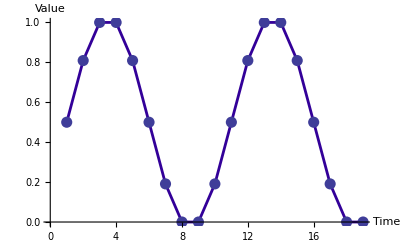

#### Partialy trained

#### Example of trained network

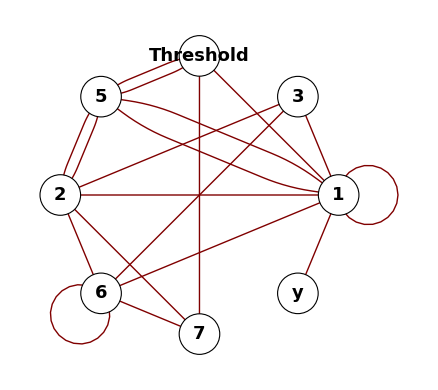

### Comparison with other methods

◀     |     ▶

## Conclusion

Continual Evolution Algorithm library

Fully Recurrent Neural Network library

#### Todo

Vizualization of population evolution in CEA (hierarchy of individuals).

Make public versions of the libraries.

#### Acknowledgements

This work is supported by the Internal Grant of Czech Technical University in Prague, IG : CTU0706813 - "Development of the Continual Evolution optimization Algorithm and its application to the artificial neural networks adaptation.

◀     |